## Subradiance-protected excitation spreading for collimated photon emission

P. Huft
See paper by K. Ballantine, J. Ruostekoski

## personal notes

### Questions

Why can a system which is excited with a single photon be adequately described by classical E&M?

The collective mode which is predominantly coupled by the initial excitation (after rotating the polarization to be normal to the atom grid plane) decays slowly, i.e. is subradiant, while other modes decay superradiantly. Why do these other modes see an a higher rate of decay than independent decay? Does it just “come out of the math” as with the √N enhancement of ensemble Rabi flopping?

How does my H_eff “know” that atomic transitions with circular light are possible? there is no defined quantization axis... maybe there should be? but then there would be zeeman splitting, which i don’t want. As it stands, all of the symmetric basis states for my diagonalized H_eff have equal occupation in all m=0 sub-states.

## setup

System description: atomnum two-level atoms arranged in a 2D square grid with equal periodicity in x and y. The lower level is has only one angular momentum state (J=0) while the upper state has three Zeeman sublevels (J=1).

```mathematica
(*PHYSICAL CONSTANTS*)
(*ℏ = 6.62607015*^-34/(2π);*)
μ0 =4π*10^-7;
c = 299792458;
ϵ0 = 1/(c^2 μ0);
ee = 1.602*^-19; (*electron charge*)
a0 = 5.27*^-11; (*Bohr radius*)
(*PARAMETERS and other DEFINITIONS*)
atomnum = 961; (*should be an odd perfect square*)
λ = 7.8*10^-7;
k=2π/λ;
matelem = ee a0; (*just assume a general matrix element is of this order for now.*)
γ = matelem^2 k^3/(6 π ϵ0); (*single two-level atom linewidth, ℏ=1*)
pol = Range[3];(*pol[[μ]]/.u->1,2,3 for polarization σ=-1,0,+1 *)
dim = atomnum;(*Hamiltonian shape is dim x dim, with state vector = dim*)

(*FUNCTIONS*)
idx[i_,j_,n_]:=(i-1)n+j//Simplify; (*get 1D atom idx from 2D coordinate indices*)
Subscript[r, i_,j_]:={0,Mod[j-1,n]-Mod[i-1,n],Floor[(j-1)/n]-Floor[(i-1)/n]}/.n->√atomnum;(*vector between atoms i,j in units lattice spacing*)
unit[v_]:=v/(√(v.v));
GdotP[r_,p_]:=ⅇ^(ⅈ k √(r.r))/(4 π √(r.r))(Cross[Cross[unit[r],p],unit[r]]+(1/(k^2 r.r)-ⅈ/(k √(r.r)))(3unit[r] Dot[unit[r],p]-p));(*r is the positional unit vector, p is an atomic dipole moment*)
Subscript[e, μ_] :={{1,0,0},{0,1,0},{0,0,1}}[[μ]];(*generic basis vector set*)
Subscript[ecart, μ_]:={1/(√2){1,0,-1}, -ⅈ/(√2){1, 0, 1}, {0, 1,0}}[[μ]];(*x,y,z in spherical basis*)
```

```mathematica
{1,0,0}.GdotP[{0,.7λ,0},{1,0,0}]
```

-11194.2-141687. ⅈ

```mathematica
{1,0,0}.GdotP[{0,λ,0},{1,0,0}]
```

99438.1+16237.4 ⅈ

```mathematica
{1,0,0}.GdotP[{0,.1λ,0},{1,0,0}]
```

-2.21974×10^6+394315. ⅈ

```mathematica
ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]
```

(102022. Cos[6.28319 √(α^2)])/(√(α^2))-(2584.26 √(α^2) Cos[6.28319 √(α^2)])/α^4-(16237.4 Sin[6.28319 √(α^2)])/α^2

```mathematica
NSolve[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]==0,α,Reals]
```

NSolve[(102022. Cos[6.28319 √(α^2)])/(√(α^2))-(2584.26 √(α^2) Cos[6.28319 √(α^2)])/α^4-(16237.4 Sin[6.28319 √(α^2)])/α^2==0,α,Reals]

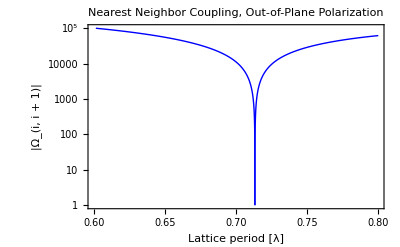

```mathematica
LogPlot[Abs[ComplexExpand[Re[{1,0,0}.GdotP[{0,α λ,0},{1,0,0}]]]],{α,0.6,.8},PlotStyle-> Directive[Blue,Thin],PlotRange->{1,100000},PlotPoints->3000,Frame->{True,True,False,False},FrameLabel->{"Lattice period [λ]","|Ω_(i, i + 1)|"},Axes->False,LabelStyle-> Directive[Black,FontSize-> 12] ,PlotLabel->Style["Nearest Neighbor Coupling, Out-of-Plane Polarization",FontSize->12]]
```

Check: does the ferromagnetic eigenmode not fully overlap a true ferromagnetic mode? In other words, does it have polarizations near zero that would allow out-of-plane emission? The in-plane mode is never very subradiant for this reason. It may be that there is an eigenmode that is very nearly a perfect ferromagnetic configuration.

Restricting this problem to the single-excitation subspace, the Hamiltonian matrix elements are: H_(3j-1+ν,3k-1+ν)=H_νμ^(jk)=Δ_μ δ_jk δ_μν+Ω_μν^(jk)(1-δ_jk)+ⅈ γ_μν^(jk), ℏ=1, where μ,ν specify polarization in a spherical basis and j,k are the atom indices in the 2D grid. The dynamics in this subspace are coherent, but H is non-Hermitian, so there is dissipation as the excitation diffuses into the collective ground state.

- Δ,γ values used are arbitrary with the given choice of plot units.

## Linewidths vs lattice spacing

```mathematica
(*in-plane state: each atom excited with P=y*)
fmode =unit[Flatten@Array[1&,atomnum]];
(*ferromagnetic state: all atoms with same polarization, in phase*)
afmode =unit[Flatten@Array[(-1)^#&,atomnum]];(*antiferromagnetic state: every atom has P=x, but alternating phases by π*)
xmodes = {Subscript[e, 1],{{fmode,"Ferromagnetic",Blue},{afmode,"Antiferromagnetic",Purple}}};
ymodes = {Subscript[e, 2],{{fmode,"In-plane",Orange}}};(*{mode, name, polarization of kth atom in cartesian basis}*)
polarizationmodes= {xmodes, ymodes};
```

```mathematica
soln=Array[{}&,Sum[Length[polarizationmodes[[n,2]]],{n,Length[polarizationmodes]}]];
lastmode =0;
runtime = Timing[
For[polmode=1,polmode<Length[polarizationmodes]+1,polmode++,
e[ν_]=polarizationmodes[[polmode,1]];
modelist = polarizationmodes[[polmode,2]];
For[d=0.01,d<1.26,d=d+0.05,(*loop over fractional lattice period*)
(*build the Hamiltonian*)
Hfull = Array[Subscript[H, ##]&,{atomnum,atomnum}];
For[i=1,i<atomnum+1,i++,
For[j=1,j<atomnum+1,j++,
u=d λ Subscript[r, i,j];
(*Gij= e[i].GdotP[u,e[j]];*)
Ωij=If[i==j,0,(6 π γ)/k Re[e[i].GdotP[u,e[j]]] ];
γij=If[i==j,γ,(6 π γ)/k Im[e[i].GdotP[u,e[j]]]];
Hfull[[i,j]]= Ωij+ⅈ γij;
];
];
{evals,evecs} = Eigensystem[Hfull];
For[mode=1,mode<Length[modelist]+1,mode++,
overlap = {};
For[i = 1,i<Length[evecs]+1,i++,
AppendTo[overlap,{i,Abs[modelist[[mode,1]].evecs[[i]]]}]
];
maxIdx=Sort[overlap,#1[[2]]>#2[[2]]&][[1,1]];
v= Im[evals[[maxIdx]]];(*mode linewidth*)
AppendTo[soln[[mode+lastmode]],{d,Log10[v/γ]}];
];(*end mode loop*)
];(*end d loop*)
lastmode=mode-1;(*since mode will increment just before the loop exits*)
];(*end pol loop*)
][[1]];
StringForm["Simulation took `` minutes",runtime/60//N]
```

Simulation took 246.087 minutes

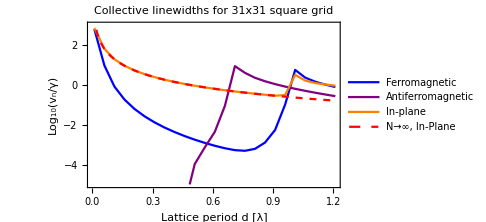

```mathematica
plots={};
lastmode=0;
For[polmode=1,polmode<Length[polarizationmodes]+1,polmode++,
modelist=polarizationmodes[[polmode,2]];
For[i=1,i<Length[modelist]+1,i++,
(*Print[i+lastmode];*)
AppendTo[plots,ListPlot[soln[[i+lastmode]],PlotRange->{-5,3},PlotStyle->modelist[[i,3]],Joined->True,PlotLegends-> {modelist[[i,2]]}]] ;
(*Print[modelist[[i,2]],modelist[[i,3]]];*)
];
lastmode=i-1;
];
AppendTo[plots,Plot[Log10[3/(4π d^2)],{d,0.02,1.21},PlotStyle->Directive[Red,Dashed],PlotLegends->{"N→∞, In-Plane"}]];
Show[plots,PlotLabel->Style[StringForm["Collective linewidths for ``x`` square grid",√atomnum,√atomnum],FontSize-> 14],ImageSize->Medium,Frame-> {True,True,False,False},FrameLabel-> {"Lattice period d [λ]","Log_10(v_n/γ)"},Axes-> False,LabelStyle-> Directive[Black,FontSize-> 12] ]
```

```mathematica
Manipulate[ListPlot[Re[evecs[[i]]],PlotStyle-> {{0,25},{-.5,.5}}],{i,Range[Length[evecs]]}]
```

## radiation in the time domain

```mathematica
(*initialize the state vector. excite central 9 atoms in m=0 states*)
(*state = Array[Subscript[b, ##]&,dim];
excitedIdcs = Flatten@Table[(atomnum-1)/2+√atomnum i+j-1,{i,{-1,0,1}},{j,{-1,0,1}}];
state[[excitedIdcs]]=1; *)
```

```mathematica
centerIdx =Floor[√atomnum/2](√atomnum+1)+1 ; (*idx of the central atom*)
```

## tests

Check my grid mapping. 2D grid, but only one index to specify atoms

```mathematica
num=√atomnum;
atom[i_,excited_]:=If[excited,Graphics[{Orange,Disk[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}],Graphics[{Blue,Circle[a{Mod[i-1,num],Floor[(i-1)/num]},0.05]}]];
r[i_,j_] :=Graphics[{Red,Line[{a{Mod[i-1,num], Floor[(i-1)/num]},a{Mod[j-1,num],Floor[(j-1)/num]}}]}];
gridpts = Table[atom[i,False],{i,Range[num^2]}];
(*excited= Table[atom[i,True],{i,Flatten@Table[(atomnum-1)/2+√atomnum i+j-1,{i,{-1,0,1}},{j,{-1,0,1}}]}];*)
positions[pts_]:=Table[r[1,j],{j,pts}]
```

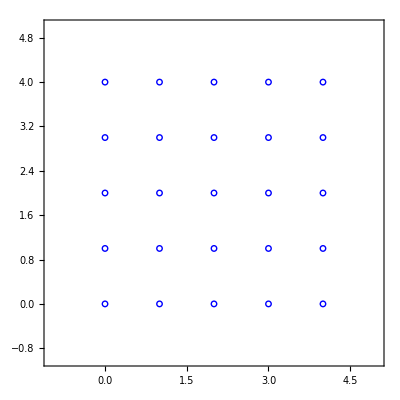

```mathematica
a=1;(*0.7;*)
showpos = {3,8,13};
Show[gridpts,(*,positions[showpos]*)PlotRange->{{-a,a num},{-a,a num}},Frame->{True,True,False,False},Axes->False]
```

What 1D atom idx corresponds to (i,j)?

```mathematica
idx[i_,j_,n_]:=(i-1)n+j//Simplify;
```

```mathematica
idx[2,2,n]
```

2+n

```mathematica
idx[1,1,n]//Simplify
```

(2+n)/2

```mathematica
Solve[{n+2== 2 (α  + β),n==α +β n },{α,β} ]
```

{{α→n^2/(2 (-1+n)),β→-(2-n)/(2 (-1+n))}}

```mathematica
Clear[i,j]
```

```mathematica
{Mod[i-1,num],Floor[(i-1)/num]}/.{i-> 2,j-> 2}
```

{1,0}

```mathematica
1/(a num)//N
```

0.0666667

```mathematica
Legended
```

```mathematica
r[i_,j_] :=a{Mod[j-1,num]-Mod[i-1,num],Floor[(j-1)/num]-Floor[(i-1)/num]};
```

```mathematica
r[1,15]
```

{2.8,1.4}

```mathematica
υ = Table[x^2+y^2,{x,{-1,0,1}},{y,{-1,0,1}}]
```

{{2,1,2},{1,0,1},{2,1,2}}

```mathematica
{1,0,1}.υ
```

{4,2,4}